```mathematica
ClearAll[nMax, modulo];
```

### Линейные зависимости в линейном конгруэнтном ГПСЧ

```mathematica
modulo = 134456(**NextPrime[10000]**);
x= 300;
y=300;
nMax= x*y;
```

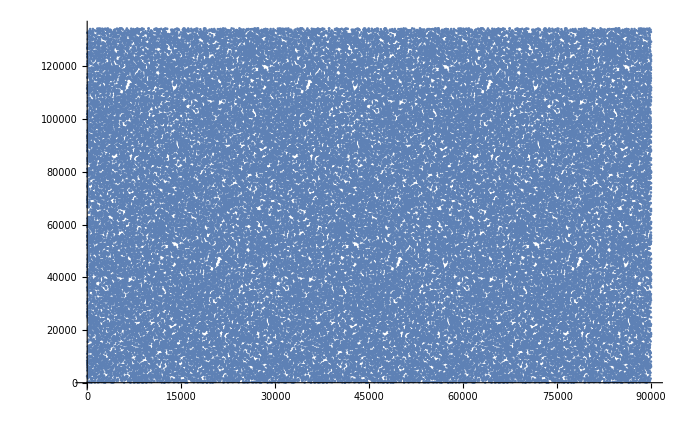

```mathematica
lkp[x_,a_,c_,m_]:=RecurrenceTable[{X[n+1]==Mod[(a* X[n]+c),m],X[1]==x},X,{n,1,nMax}];
congruentBlock = lkp[0,859,2531,modulo];
ListPlot[congruentBlock]
```

```mathematica
ListPointPlot3D[ArrayReshape[congruentBlock,{x,y}]]
```

-Graphics3D-

### Отсутствие линейных зависисмостей в ГПСЧ Мерсенна

```mathematica
block = BlockRandom[SeedRandom[1,Method->"MersenneTwister"];RandomInteger[modulo, nMax]];
```

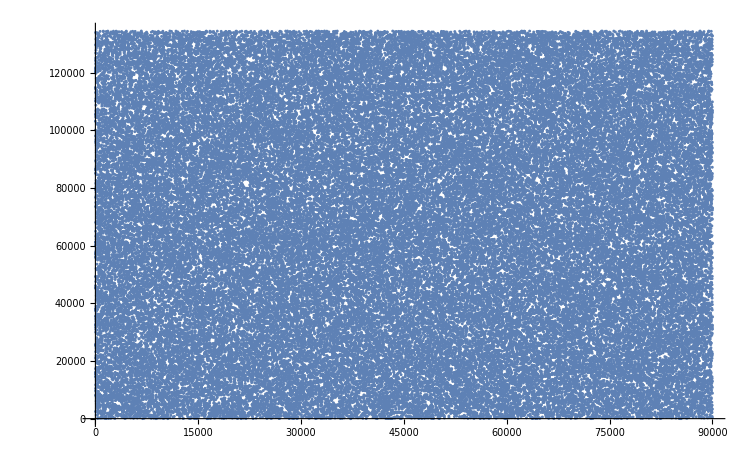

```mathematica
ListPlot[block]
```

```mathematica
ListPointPlot3D[ArrayReshape[block,{x,y}]]
```

-Graphics3D-